```mathematica
vgg=NetModel["VGG-16 Trained on ImageNet Competition Data"];
```

```mathematica
folderName = "/Users/Anatoly/Documents/OneDrive/Documents/Personal/Projects/For Yves/fast.ai/";
```

```mathematica
fileNames=FileNameJoin[{folderName,#}]&/@{"164807-horses-horse.jpg","brown_horse.jpg","Megelli_Sports_motorcycle.jpg","Moto_Guzzi_Italian_motorcycle.jpg"};
```

```mathematica
imageSet=Import/@fileNames
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
vgg[imageSet]
```

{Rhodesian ridgeback,sorrel,moped,moped}

```mathematica
outputLayers={"flatten_0","relu6","relu7","fc8"};
```

```mathematica
featureNet=Take[vgg,{1,outputLayers[[1]]}];
```

```mathematica
features=featureNet[imageSet];
```

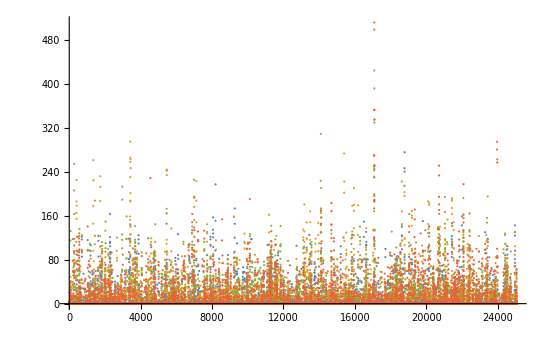

```mathematica
ListPlot[features]
```

```mathematica
dm=DistanceMatrix[features]
```

{{0.,2663.1,3028.89,3135.7},{2663.1,0.,3461.6,3549.93},{3028.89,3461.6,0.,2466.73},{3135.7,3549.93,2466.73,0.}}

```mathematica
dm//MatrixForm
```

(0. | 2663.1 | 3028.89 | 3135.7
2663.1 | 0. | 3461.6 | 3549.93
3028.89 | 3461.6 | 0. | 2466.73
3135.7 | 3549.93 | 2466.73 | 0.)